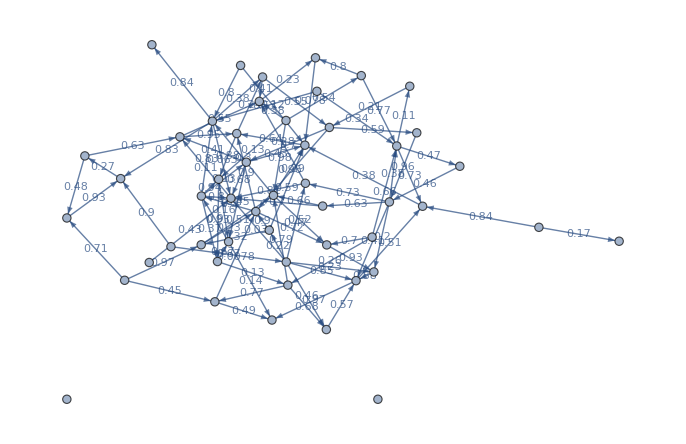

```mathematica
ClearAll["Global`*"]
nVertex=50;
nEdges=2nVertex;
graph=RandomGraph[{nVertex,nEdges}, DirectedEdges->True, EdgeWeight->Table[RandomReal[{0,1}, WorkingPrecision->2], {i, nEdges}],EdgeLabels->"EdgeWeight"]
```

```mathematica
shortest=FindShortestPath[graph,1,nVertex-4]
```

{1,2,21,37,7,45,31,36,19,5,16,46}

```mathematica
EdgeW=AnnotationValue[graph,EdgeWeight]
EdgeL=EdgeList[graph]
coord=AbsoluteOptions[graph, VertexCoordinates][[1]][[2]]
```

{0.23,0.078,0.0078,0.49,0.27,0.38,0.41,0.73,0.2,0.63,0.41,0.55,0.3,0.96,0.52,0.43,0.84,0.17,0.38,0.9,0.67,0.11,0.57,0.68,0.43,0.41,0.45,0.63,0.48,0.73,0.11,0.47,0.51,0.97,0.84,0.83,0.38,0.063,0.13,0.67,0.64,0.28,0.81,0.34,0.53,0.88,0.59,0.32,0.9,0.8,0.12,0.21,0.55,0.95,0.51,0.23,0.3,0.9,0.72,0.77,0.79,0.68,0.46,0.8,0.77,0.38,0.98,0.54,0.13,0.8,0.13,0.83,0.37,0.94,0.24,0.88,0.96,0.45,0.97,0.71,0.93,0.16,0.93,0.031,0.46,0.85,0.47,0.23,0.22,0.66,0.26,0.7,0.7,0.29,0.59,0.93,0.66,0.7,0.9,0.14}

{1->2,2->21,4->31,4->43,5->16,6->17,6->18,6->22,6->24,6->48,7->1,7->45,8->19,8->21,8->41,9->13,10->11,10->47,11->21,12->5,12->42,13->29,14->18,15->13,15->21,15->29,15->50,16->29,16->46,17->11,17->28,17->33,18->11,18->43,19->3,19->5,19->7,19->13,20->32,20->50,21->37,22->1,22->13,23->17,23->19,24->18,25->21,25->30,25->31,27->19,27->21,28->45,29->1,29->37,30->8,30->31,31->36,31->37,31->41,32->4,32->8,32->14,33->6,34->2,34->17,35->1,35->8,35->34,35->40,36->13,36->15,36->19,36->20,36->40,37->7,37->40,38->6,39->4,39->30,39->46,40->20,40->50,41->24,42->13,42->14,42->18,42->22,42->24,42->25,44->17,44->32,44->41,45->15,45->31,45->38,46->5,48->8,48->13,50->36,50->43}

{{2.92624,-1.17907},{3.64896,-0.617248},{1.54367,-0.449122},{2.35385,-3.76192},{1.1417,-2.17441},{4.60073,-2.4749},{2.9684,-0.86481},{3.10858,-2.39013},{1.50917,-3.25551},{6.5246,-2.80181},{5.02786,-2.53053},{1.78903,-3.05116},{2.56057,-2.42728},{3.7888,-4.11958},{2.75845,-1.96291},{0.680911,-1.88156},{4.69497,-1.7543},{4.17087,-3.48961},{2.3224,-1.43416},{2.38773,-3.24291},{3.51283,-1.74366},{3.51937,-2.23457},{3.66739,-1.0491},{4.40088,-3.37716},{3.05425,-2.83881},{0.449122,-5.01782},{2.68538,-0.715569},{4.8627,-0.983934},{1.90414,-1.63556},{2.17819,-3.02721},{2.88108,-2.5983},{3.29403,-3.54695},{5.50687,-2.01505},{4.23863,-0.847145},{3.26953,-1.42527},{2.18027,-2.39899},{2.63563,-1.59374},{4.95266,-1.58389},{1.1929,-3.48448},{2.40297,-2.18286},{3.794,-3.02869},{3.27317,-3.24921},{3.08915,-3.99688},{4.37766,-2.92786},{3.82763,-1.51472},{0.449122,-2.68167},{7.55735,-2.98135},{3.74151,-2.52823},{4.45236,-5.01782},{2.5306,-2.98725}}

```mathematica
export=Join[{nVertex},coord,{nEdges},Table[{EdgeL[[i]][[1]],EdgeL[[i]][[2]], EdgeW[[i]]}, {i,1,nEdges}], {1},{{First[shortest],Last[shortest]}}];

SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["problem.txt",export, "Table"]
Export["solution.txt", {1,shortest}, "Table"]
```

problem.txt

solution.txt